```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"foot_naive.xml"];*)
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

targets=<|2->{0.2,0.8},3->{0.1,0.3,0.6},4->{0.1,0.2,0.3,0.4}|>;
target=targets[Length[index0]]
CloseKernels[];
LaunchKernels[8];
Clear[f];
Clear[data];
records={};
```

{0.1,0.3,0.6}

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
epsilon=0.01;
stepsize=0.05;
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,50}];
```

2.050462

37

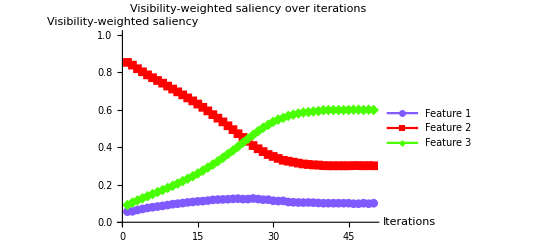

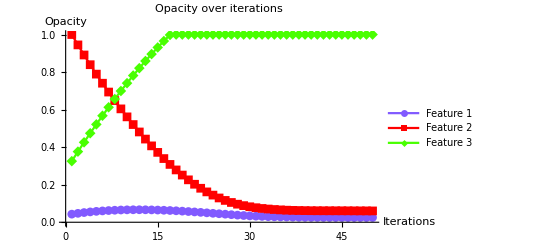

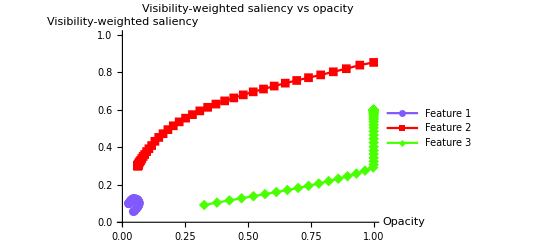

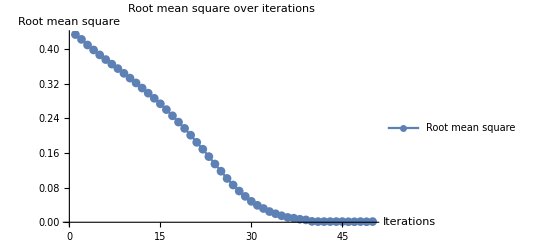

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197
2 | 0.0581638
0.837143
0.104693 | 0.0474719
0.944846
0.37631 | 0.422533 | 0.00418362
-0.0537143
0.0495307
3 | 0.0654655
0.817979
0.116555 | 0.0516555
0.891131
0.425841 | 0.409558 | 0.00345345
-0.0517979
0.0483445
4 | 0.0708222
0.80149
0.127688 | 0.0551089
0.839333
0.474185 | 0.398088 | 0.00291778
-0.050149
0.0472312
5 | 0.0762826
0.785044
0.138673 | 0.0580267
0.789184
0.521416 | 0.386718 | 0.00237174
-0.0485044
0.0461327
6 | 0.0799996
0.77006
0.14994 | 0.0603985
0.74068
0.567549 | 0.375903 | 0.00200004
-0.047006
0.045006
7 | 0.0837749
0.755361
0.160864 | 0.0623985
0.693674
0.612555 | 0.365357 | 0.00162251
-0.0455361
0.0439136
8 | 0.0871895
0.741114
0.171697 | 0.064021
0.648138
0.656468 | 0.355053 | 0.00128105
-0.0441114
0.0428303
9 | 0.0916191
0.725596
0.182784 | 0.0653021
0.604027
0.699299 | 0.344128 | 0.000838085
-0.0425596
0.0417216
10 | 0.0961713
0.709785
0.194044 | 0.0661402
0.561467
0.74102 | 0.333036 | 0.000382873
-0.0409785
0.0405956
11 | 0.0989591
0.694723
0.206318 | 0.066523
0.520488
0.781616 | 0.321866 | 0.000104089
-0.0394723
0.0393682
12 | 0.102156
0.678634
0.219211 | 0.0666271
0.481016
0.820984 | 0.310037 | -0.000215569
-0.0378634
0.0380789
13 | 0.105694
0.662417
0.231888 | 0.0664115
0.443153
0.859063 | 0.298264 | -0.000569441
-0.0362417
0.0368112
14 | 0.10825
0.646587
0.245163 | 0.0658421
0.406911
0.895874 | 0.286414 | -0.000825002
-0.0346587
0.0354837
15 | 0.111029
0.629578
0.259393 | 0.0650171
0.372252
0.931358 | 0.273713 | -0.00110294
-0.0329578
0.0340607
16 | 0.112599
0.612288
0.275113 | 0.0639142
0.339295
0.965419 | 0.260278 | -0.00125988
-0.0312288
0.0324887
17 | 0.115403
0.593264
0.291332 | 0.0626543
0.308066
0.997907 | 0.245979 | -0.00154034
-0.0293264
0.0308668
18 | 0.119169
0.57335
0.307482 | 0.0611139
0.278739
1. | 0.231412 | -0.00191686
-0.027335
0.0292518
19 | 0.120713
0.554617
0.32467 | 0.0591971
0.251404
1. | 0.216845 | -0.0020713
-0.0254617
0.027533
20 | 0.121703
0.534789
0.343507 | 0.0571258
0.225943
1. | 0.201151 | -0.00217035
-0.0234789
0.0256493
21 | 0.122797
0.513904
0.363299 | 0.0549554
0.202464
1. | 0.184664 | -0.00227972
-0.0213904
0.0236701
22 | 0.124558
0.49332
0.382123 | 0.0526757
0.181073
1. | 0.168766 | -0.00245576
-0.019332
0.0217877
23 | 0.125629
0.471666
0.402705 | 0.05022
0.161741
1. | 0.151714 | -0.00256289
-0.0171666
0.0197295
24 | 0.123313
0.451925
0.424762 | 0.0476571
0.144575
1. | 0.134577 | -0.00233134
-0.0151925
0.0175238
25 | 0.123346
0.431359
0.445295 | 0.0453257
0.129382
1. | 0.117946 | -0.00233465
-0.0131359
0.0154705
26 | 0.126664
0.408499
0.464837 | 0.0429911
0.116246
1. | 0.101246 | -0.00266642
-0.0108499
0.0135163
27 | 0.123628
0.391589
0.484783 | 0.0403247
0.105397
1. | 0.0860657 | -0.00236277
-0.00915895
0.0115217
28 | 0.120228
0.376422
0.503349 | 0.0379619
0.0962376
1. | 0.07209 | -0.00202284
-0.00764223
0.00966507
29 | 0.120384
0.360899
0.518716 | 0.0359391
0.0885953
1. | 0.0598088 | -0.00203845
-0.00608992
0.00812837
30 | 0.114544
0.350543
0.534913 | 0.0339006
0.0825054
1. | 0.0483129 | -0.00145444
-0.00505426
0.00650869
31 | 0.112952
0.340083
0.546965 | 0.0324462
0.0774512
1. | 0.0391028 | -0.00129521
-0.00400828
0.0053035
32 | 0.113707
0.330202
0.55609 | 0.031151
0.0734429
1. | 0.0317706 | -0.00137072
-0.00302023
0.00439095
33 | 0.107998
0.325453
0.56655 | 0.0297803
0.0704226
1. | 0.0247031 | -0.000799765
-0.00254527
0.00334503
34 | 0.10629
0.3203
0.57341 | 0.0289805
0.0678774
1. | 0.019653 | -0.000629027
-0.00203002
0.00265905
35 | 0.105409
0.315047
0.579544 | 0.0283515
0.0658474
1. | 0.0149903 | -0.000540859
-0.00150475
0.00204561
36 | 0.104814
0.310572
0.584614 | 0.0278106
0.0643426
1. | 0.0111304 | -0.000481416
-0.00105716
0.00153858
37 | 0.105271
0.307925
0.586805 | 0.0273292
0.0632854
1. | 0.00939323 | -0.000527088
-0.000792451
0.00131954
38 | 0.104417
0.305398
0.590186 | 0.0268021
0.062493
1. | 0.0069513 | -0.00044167
-0.000539759
0.000981429
39 | 0.102761
0.304817
0.592421 | 0.0263604
0.0619532
1. | 0.00542415 | -0.000276141
-0.000481712
0.000757853
40 | 0.101244
0.301616
0.59714 | 0.0260843
0.0614715
1. | 0.00202798 | -0.000124384
-0.000161609
0.000285993
41 | 0.101356
0.300778
0.597866 | 0.0259599
0.0613099
1. | 0.00152741 | -0.000135634
-0.0000777762
0.00021341
42 | 0.101356
0.300778
0.597866 | 0.0258243
0.0612321
1. | 0.00152741 | -0.000135634
-0.0000777762
0.00021341
43 | 0.101356
0.300778
0.597866 | 0.0256886
0.0611544
1. | 0.00152741 | -0.000135634
-0.0000777762
0.00021341
44 | 0.101356
0.300778
0.597866 | 0.025553
0.0610766
1. | 0.00152741 | -0.000135634
-0.0000777762
0.00021341
45 | 0.101356
0.300778
0.597866 | 0.0254174
0.0609988
1. | 0.00152741 | -0.000135634
-0.0000777762
0.00021341
46 | 0.0988185
0.301546
0.599635 | 0.0252817
0.060921
1. | 0.00114311 | 0.000118153
-0.00015463
0.0000364768
47 | 0.0988185
0.301546
0.599635 | 0.0253999
0.0607664
1. | 0.00114311 | 0.000118153
-0.00015463
0.0000364768
48 | 0.101356
0.300778
0.597866 | 0.025518
0.0606118
1. | 0.00152741 | -0.000135634
-0.0000777762
0.00021341
49 | 0.0988185
0.301546
0.599635 | 0.0253824
0.060534
1. | 0.00114311 | 0.000118153
-0.00015463
0.0000364768
50 | 0.101356
0.300778
0.597866 | 0.0255006
0.0603794
1. | 0.00152741 | -0.000135634
-0.0000777762
0.00021341

```mathematica
t2-t1
iteration
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity1=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliency_opacity_fixed.png",saliencyopacity1];
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_fixed.png",table1];
(*path1=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

```mathematica
(*alpha0[[#]]&/@index0
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0]*)
(*(*first order newton*)
target={0.1,0.3,0.6};
stepsize=0.1;
previous={{0,0,0},{0,0,0}};
list=Table[Module[{peaks,mean,steps,rms,f1,f0,diff,square,derivative,xx,dx,yy,df,factor},
mean=visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
derivative=2*(mean-target);
square=(mean-target)^2;
If[Norm[First@previous]>0,{f1,f0,xx,yy}=previous,{f1,f0,xx,yy}={derivative,square,peaks,mean}];
(*diff=mean-y1;
steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,(target-mean)*(peaks-x1)/(mean-y1)*stepsize,2*(target-mean)*stepsize];*)
(*dx=peaks-xx;
df=If[Product[dx[[i]],{i,Length[dx]}]≠0,(mean-yy)/dx,1];*)
(*derivative=derivative*df;*)
diff=derivative-f1;
previous={derivative,square,peaks,mean};
df=If[Product[diff[[i]],{i,Length[diff]}]≠0,-(square-f0)/diff*stepsize,-derivative*stepsize];(*should be second-order but look like first-order*)
dx=-derivative*stepsize;
steps=Table[If[Abs[dx[[i]]]>Abs[df[[i]]],dx[[i]],df[[i]]],{i,Length[mean]}];
(*steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,-derivative*(peaks-xx)/diff*stepsize,-derivative*stepsize];*)
(*steps=-derivative*stepsize;*)
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
{mean,peaks,rms,steps,dx,df,Table[Abs[df[[i]]]>Abs[dx[[i]]],{i,Length[dx]}]}
],{30}];*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

0.4683313

4

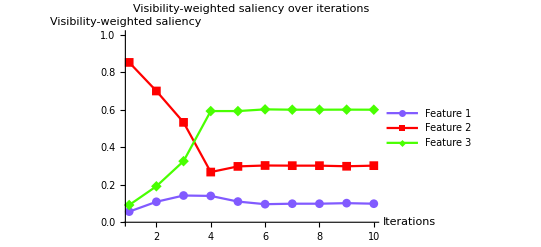

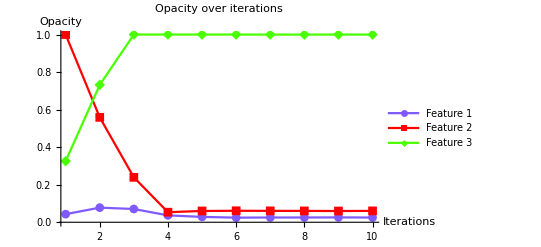

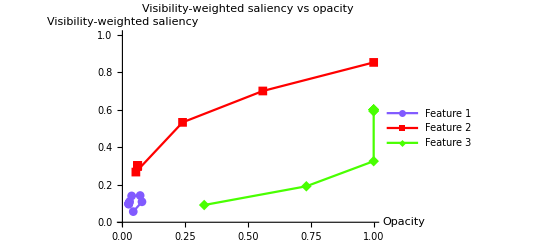

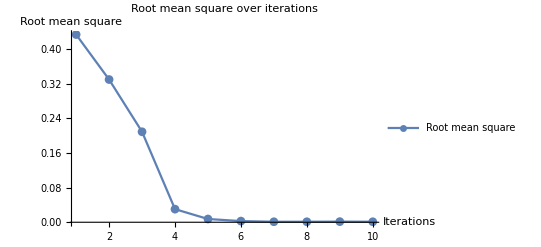

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | 8
2 | 0.109027
0.699312
0.191661 | 0.0778142
0.558766
0.732048 | 0.329784 | -0.000902683
-0.0399312
0.0408339 | 8
3 | 0.14244
0.532157
0.325404 | 0.0705928
0.239316
1. | 0.209046 | -0.00424397
-0.0232157
0.0274596 | 8
4 | 0.1403
0.267363
0.592337 | 0.036641
0.0535909
1. | 0.0302657 | -0.00403004
0.00326373
0.000766308 | 2
5 | 0.11017
0.297563
0.592268 | 0.0285809
0.0601183
1. | 0.00750894 | -0.00101696
0.000243719
0.000773246 | 4
6 | 0.0962455
0.302352
0.601402 | 0.024513
0.0610932
1. | 0.00268298 | 0.000375448
-0.000235207
-0.000140242 | 2
7 | 0.0988119
0.301527
0.599661 | 0.0252639
0.0606228
0.99972 | 0.00113431 | 0.000118814
-0.000152747
0.0000339327 | 1
8 | 0.0988119
0.301527
0.599661 | 0.0253828
0.0604701
0.999753 | 0.00113431 | 0.000118814
-0.000152747
0.0000339327 | 4
9 | 0.101768
0.298279
0.599953 | 0.025858
0.0598591
0.999889 | 0.00142493 | -0.000176812
0.000172128
4.68348×10^-6 | 4
10 | 0.0988185
0.301546
0.599635 | 0.0251508
0.0605476
0.999908 | 0.00114311 | 0.000118153
-0.00015463
0.0000364768 | 1

```mathematica
t2-t1
iteration
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity2=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliency_opacity_parallelsearch.png",saliencyopacity2];
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_parallelsearch.png",table2];
(*path2=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

0.9086558

4

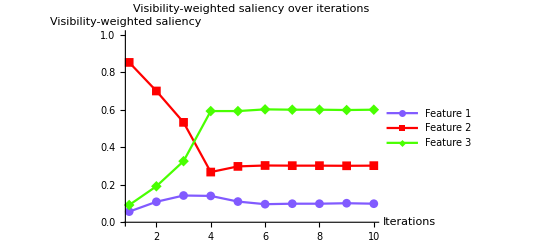

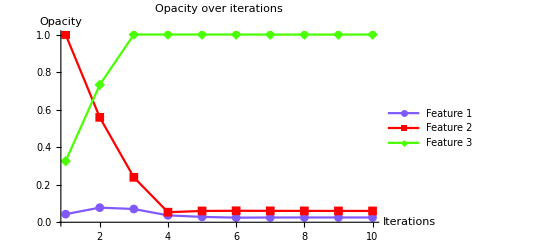

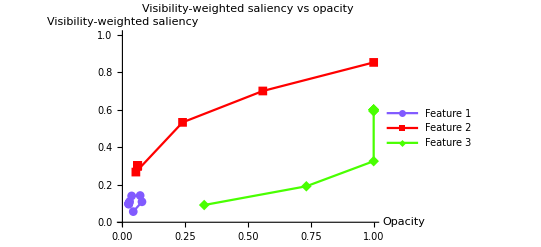

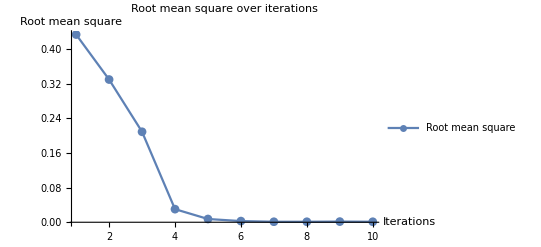

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | 8
2 | 0.109027
0.699312
0.191661 | 0.0778142
0.558766
0.732048 | 0.329784 | -0.000902683
-0.0399312
0.0408339 | 8
3 | 0.14244
0.532157
0.325404 | 0.0705928
0.239316
1. | 0.209046 | -0.00424397
-0.0232157
0.0274596 | 8
4 | 0.1403
0.267363
0.592337 | 0.036641
0.0535909
1. | 0.0302657 | -0.00403004
0.00326373
0.000766308 | 2
5 | 0.11017
0.297563
0.592268 | 0.0285809
0.0601183
1. | 0.00750894 | -0.00101696
0.000243719
0.000773246 | 4
6 | 0.0962455
0.302352
0.601402 | 0.024513
0.0610932
1. | 0.00268298 | 0.000375448
-0.000235207
-0.000140242 | 2
7 | 0.0988119
0.301527
0.599661 | 0.0252639
0.0606228
0.99972 | 0.00113431 | 0.000118814
-0.000152747
0.0000339327 | 1
8 | 0.0988119
0.301527
0.599661 | 0.0253828
0.0604701
0.999753 | 0.00113431 | 0.000118814
-0.000152747
0.0000339327 | 1
9 | 0.10135
0.300759
0.597891 | 0.0255016
0.0603173
0.999787 | 0.00151037 | -0.000134956
-0.000075903
0.000210859 | 1
10 | 0.0988185
0.301546
0.599635 | 0.0253666
0.0602414
0.999998 | 0.00114311 | 0.000118153
-0.00015463
0.0000364768 | 1

```mathematica
t2-t1
iteration
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity3=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliency_opacity_linesearch.png",saliencyopacity3];
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_linesearch.png",table3];
(*path3=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

```mathematica
recordxml=NotebookDirectory[]<>"~images\\records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

nucleon_strong_red→{{2.050462,37,{0.0255006,0.0603794,1.}},{0.4683313,4,{0.0251508,0.0605476,0.999908}},{0.9086558,4,{0.0253666,0.0602414,0.999998}}}

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
Clear[f];
Clear[data];
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[NotebookDirectory[]<>dataname<>"_parameterspace.png",sp];
Export[NotebookDirectory[]<>dataname<>"_parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[NotebookDirectory[]<>dataname<>"_densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],NotebookDirectory[]<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],NotebookDirectory[]<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],NotebookDirectory[]<>dataname<>"_optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics3D-

-Graphics3D-

-Graphics-

-Graphics-